```mathematica
S[α_]:=({{1, 0}, {α, 1}}); A:=({{0, -ⅈ}, {-ⅈ, 0}}); W[Φ_]:=({{E^Φ, 0}, {0, E^-Φ}});
line[a_,b_]:=Function[t,a+(b-a)t];
```

{{z→-1.-1.73205 ⅈ},{z→-1.+1.73205 ⅈ},{z→0.},{z→2.}}

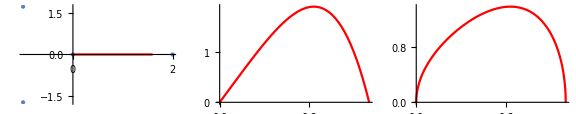

0.+1.0472 ⅈ

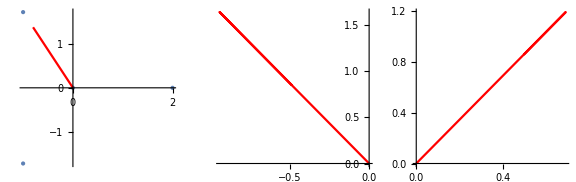

-0.9069+0.523599 ⅈ

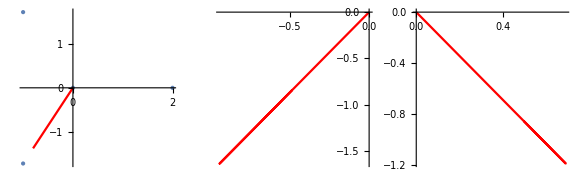

0.9069+0.523599 ⅈ

```mathematica
δ=0; U=Function[p,(8p-(p^2-δ^2)^2)/4]; zeros=NSolve[U[z]==0,z]
oa=line[z/.zeros[[3]],z/.zeros[[4]]];
ListPlot[Table[{Re[z/.zeros[[i]]],Im[z/.zeros[[i]]]},{i,1,Length[zeros]}],PlotStyle->PointSize[Large],PlotRange->Full];
ParametricPlot[{Re[oa[t]],Im[oa[t]]},{t,0,0.8},PlotStyle->{Red}];
Plot[Re[U[oa[t]]],{t,0,1},PlotStyle->{Red}];
Plot[√U[oa[t]],{t,0,1},PlotStyle->{Red}];
GraphicsRow[{Show[%%%%,%%%],%%,%},ImageSize->Large]
NIntegrate[ⅈ √U[oa[t]],{t,0,1}]

ob=line[z/.zeros[[3]],z/.zeros[[2]]];
ListPlot[Table[{Re[z/.zeros[[i]]],Im[z/.zeros[[i]]]},{i,1,Length[zeros]}],PlotStyle->PointSize[Large],PlotRange->Full];
ParametricPlot[{Re[ob[t]],Im[ob[t]]},{t,0,0.8},PlotStyle->{Red}];
ParametricPlot[{Re[U[ob[t]]],Im[U[ob[t]]]},{t,0,0.9},PlotStyle->{Red}];
ParametricPlot[{Re[√U[ob[t]]],Im[√U[ob[t]]]},{t,0,0.9},PlotStyle->{Red}];
GraphicsRow[{Show[%%%%,%%%],%%,%},ImageSize->Large]
NIntegrate[ⅈ √U[ob[t]],{t,0,1}]

oc=line[z/.zeros[[3]],z/.zeros[[1]]];
ListPlot[Table[{Re[z/.zeros[[i]]],Im[z/.zeros[[i]]]},{i,1,Length[zeros]}],PlotStyle->PointSize[Large],PlotRange->Full];
ParametricPlot[{Re[oc[t]],Im[oc[t]]},{t,0,0.8},PlotStyle->{Red}];
ParametricPlot[{Re[U[oc[t]]],Im[U[oc[t]]]},{t,0,0.9},PlotStyle->{Red}];
ParametricPlot[{Re[√U[oc[t]]],Im[√U[oc[t]]]}/.x->oc[t],{t,0,0.9},PlotStyle->{Red}];
GraphicsRow[{Show[%%%%,%%%],%%,%},ImageSize->Large]
NIntegrate[ⅈ √U[oc[t]],{t,0,1}]
```

```mathematica
S[a6/2].A.W[-OB].S[a5]ᵀ.S[a4].A.S[a3].W[OB].S[a2].W[-OA].S[a1].S[a0/2]ᵀ;
S[-b6/2].W[-OC].S[-b5].S[-b4]ᵀ.A*.S[-b3]ᵀ.W[OC].S[-b2]ᵀ.W[-OA].S[-b1]ᵀ.A*.S[-a0/2]ᵀ;
FullSimplify[(%%-%)]//MatrixForm
```

(ⅇ^(-OA-2 OC) ((1+b3 b4) ⅇ^(2 OA)+(-a2 a4+b1 b4) ⅇ^(2 OC)+(-a1 a4+b2 b4) ⅇ^(2 (OA+OC))-(1+a3 a4) ⅇ^(2 (OB+OC))) | 1/2 ⅇ^(-OA-2 OC) (-2 ⅇ^(2 OC) (b4+a4 ⅇ^(2 OA))-a0 ((1+b3 b4) ⅇ^(2 OA)+(a2 a4+b1 b4) ⅇ^(2 OC)+(a1 a4+b2 b4) ⅇ^(2 (OA+OC))+(1+a3 a4) ⅇ^(2 (OB+OC))))
1/2 ⅇ^(-OA-2 (OB+OC)) (-(1+b3 b4) b6 ⅇ^(2 (OA+OB))-2 (1+b4 b5) ⅇ^(2 OB+4 OC) (b1+b2 ⅇ^(2 OA))+ⅇ^(2 OC) (-(2 a5+2 a3 (1+a4 a5)+a2 a4 a6+b1 b4 b6) ⅇ^(2 OB)-(1+a3 a4) a6 ⅇ^(4 OB)-(a1 a4 a6+2 (b3+b5+b3 b4 b5)+b2 b4 b6) ⅇ^(2 (OA+OB))-2 (1+a4 a5) (a2+a1 ⅇ^(2 OA)))) | 1/4 ⅇ^(-OA-2 (OB+OC)) (a0 (1+b3 b4) b6 ⅇ^(2 (OA+OB))+2 (1+b4 b5) ⅇ^(2 OB+4 OC) (2+a0 (b1+b2 ⅇ^(2 OA)))+ⅇ^(2 OC) (-a0 (1+a3 a4) a6 ⅇ^(4 OB)-2 (1+a4 a5) (a0 a2+(2+a0 a1) ⅇ^(2 OA))+ⅇ^(2 OB) (2 b4 b6-a0 (2 a5+2 a3 (1+a4 a5)+a2 a4 a6-b1 b4 b6)+(-(2+a0 a1) a4 a6+2 a0 (b3+b5+b3 b4 b5)+a0 b2 b4 b6) ⅇ^(2 OA)))))

```mathematica
constants=Solve[{
b3 b4==-1,
a2 a4==b1 b4,
a1 a4==b2 b4,
a3 a4==-1,
b4 b5==-1,
a4 a5==-1,
2 a5+a2 a4 a6+b1 b4 b6==0,
a1 a4 a6+2 (b3+b5+b3 b4 b5)+b2 b4 b6==0,
2 b4 b6-a0 (2 a5+a2 a4 a6-b1 b4 b6)==0,
-(2+a0 a1) a4 a6+2 a0 (b3+b5+b3 b4 b5)+a0 b2 b4 b6==0,
2b4+a0 (a2 a4+b1 b4)==0,
2a4+a0(a1 a4+b2 b4)==0,
a6==b6},{a0,a1,a2,a3,a4,a5,a6,b0,b1,b2,b3,b4,b5,b6}][[1]]
```

{a1→-1/a0,a2→-b4/(a0 a4),a3→-1/a4,a5→-1/a4,a6→-a0/(a4 b4),b1→-1/a0,b2→-a4/(a0 b4),b3→-1/b4,b5→-1/b4,b6→-a0/(a4 b4)}

```mathematica
FullSimplify[S[a0]ᵀ.A.S[b1]ᵀ.W[OA].S[b2]ᵀ.W[-OC].S[b3]ᵀ.A.S[b4]ᵀ.S[b5].W[OC].S[a6].A.W[-OB].S[a5]ᵀ.S[a4].A.S[a3].W[OB].S[a2].W[-OA].S[a1]/.constants]//MatrixForm
```

(1 | 0
0 | 1)

```mathematica
S[a6/2].A.W[-OB].S[a5]ᵀ.S[a4].A.S[a3].W[OB].S[a2].W[-OA].S[a1].S[a0/2]ᵀ/.constants;
S[-b6/2].W[-OC].S[-b5].S[-b4]ᵀ.A*.S[-b3]ᵀ.W[OC].S[-b2]ᵀ.W[-OA].S[-b1]ᵀ.A*.S[-a0/2]ᵀ/.constants;
FullSimplify[(%%-%)]//MatrixForm
```

(0 | 0
0 | 0)

```mathematica
FullSimplify[S[b4/2]ᵀ.S[b5].W[OC].S[a6].W[-OB].S[a5].S[a4/2]ᵀ.({{1}, {0}})/.constants]//MatrixForm
```

((ⅇ^(-OB-OC) (-a0-b4 ⅇ^(2 OB)+a4 ⅇ^(2 OC)))/(2 a4)
-(ⅇ^(-OB-OC) (a0+b4 ⅇ^(2 OB)+a4 ⅇ^(2 OC)))/(a4 b4))

```mathematica
SubPlus[a]=S[Subscript[α, 6]].W[ca].S[Subscript[α, 5]].S[Subscript[α, 4]]ᵀ.W[ab*].S[Subscript[α, 3]]ᵀ.S[Subscript[α, 2]].W[ab].S[Subscript[α, 1]].({{1}, {0}})//Simplify;SubMinus[a]=S[Subscript[α, -6]]ᵀ.W[-ab].S[Subscript[α, -5]]ᵀ.S[Subscript[α, -4]].W[-ab*].S[Subscript[α, -3]].S[Subscript[α, -2]]ᵀ.W[-ca].S[Subscript[α, -1]]ᵀ.({{1}, {0}})//Simplify;
({{1, 1, Log[z]}, {ⅈ(SubPlus[a]⟦1,1⟧ⅇ^(4/3 z^(3/2))+SubPlus[a]⟦2,1⟧), -1, -(Log[z]-2ⅈ π)}, {-ⅈ(SubMinus[a]⟦1,1⟧ⅇ^(4/3 z^(3/2))+SubMinus[a]⟦2,1⟧), -1, -(Log[z]+2ⅈ π)}})//Det//Simplify
```

-2 ⅇ^(-ab-ca-Conjugate[ab]) π (-ⅇ^((4 z^(3/2))/3)-2 ⅈ ⅇ^(ab+ca+Conjugate[ab])+ⅇ^(2 ab+2 ca+(4 z^(3/2))/3+2 Conjugate[ab])-(ⅇ^(2 ab)+ⅇ^(2 ab+(4 z^(3/2))/3) α_-6+ⅇ^((4 z^(3/2))/3) α_-5) α_-4-ⅇ^(2 Conjugate[ab]) (ⅇ^(2 ab)+ⅇ^(2 ab+(4 z^(3/2))/3) α_-6+ⅇ^((4 z^(3/2))/3) α_-5) α_-3+α_1+ⅇ^(2 ab) α_2+ⅇ^(2 ca+(4 z^(3/2))/3+2 Conjugate[ab]) α_1 α_3+ⅇ^(2 ab+2 ca+(4 z^(3/2))/3+2 Conjugate[ab]) α_2 α_3+ⅇ^(2 ca+(4 z^(3/2))/3) α_1 α_4+ⅇ^(2 ab+2 ca+(4 z^(3/2))/3) α_2 α_4+ⅇ^(2 (ab+Conjugate[ab])) α_5+ⅇ^(2 Conjugate[ab]) α_1 α_3 α_5+ⅇ^(2 (ab+Conjugate[ab])) α_2 α_3 α_5+α_1 α_4 α_5+ⅇ^(2 ab) α_2 α_4 α_5+ⅇ^(2 (ab+ca+Conjugate[ab])) α_6+ⅇ^(2 (ca+Conjugate[ab])) α_1 α_3 α_6+ⅇ^(2 (ab+ca+Conjugate[ab])) α_2 α_3 α_6+ⅇ^(2 ca) α_1 α_4 α_6+ⅇ^(2 (ab+ca)) α_2 α_4 α_6)

```mathematica
ⅇ^(2 i)-1-(Subscript[α, -6] ⅇ^(2ab)+Subscript[α, -5])Subscript[α, -4]-ⅇ^(2 bc) (ⅇ^(2 ab) Subscript[α, -6]+Subscript[α, -5]) Subscript[α, -3]+ⅇ^(2 bc+2 ca) Subscript[α, 1] Subscript[α, 3]+ⅇ^(2 i) Subscript[α, 2] Subscript[α, 3]+ⅇ^(2 ca) Subscript[α, 1] Subscript[α, 4]+ⅇ^(2 ab+2 ca) Subscript[α, 2] Subscript[α, 4]//Simplify
-2 ⅈ ⅇ^i-ⅇ^(2 ab) Subscript[α, -4]-ⅇ^(2 bc) ⅇ^(2 ab) Subscript[α, -3]+Subscript[α, 1]+ⅇ^(2 ab) Subscript[α, 2]++ⅇ^(2 (ab+bc)) Subscript[α, 5]+ⅇ^(2 bc) Subscript[α, 1] Subscript[α, 3] Subscript[α, 5]+ⅇ^(2 (ab+bc)) Subscript[α, 2] Subscript[α, 3] Subscript[α, 5]+Subscript[α, 1] Subscript[α, 4] Subscript[α, 5]+ⅇ^(2 ab) Subscript[α, 2] Subscript[α, 4] Subscript[α, 5]+ⅇ^(2 i) Subscript[α, 6]+ⅇ^(2 (bc+ca)) Subscript[α, 1] Subscript[α, 3] Subscript[α, 6]+ⅇ^(2 i) Subscript[α, 2] Subscript[α, 3] Subscript[α, 6]+ⅇ^(2 ca) Subscript[α, 1] Subscript[α, 4] Subscript[α, 6]+ⅇ^(2 (ab+ca)) Subscript[α, 2] Subscript[α, 4] Subscript[α, 6]//Simplify
```

```mathematica
(ⅇ^(2 i) Subscript[α, 2] Subscript[α, 3]+ⅇ^(2 ca) (ⅇ^(2 ab*) Subscript[α, 1] Subscript[α, 3]+Subscript[α, 1] Subscript[α, 4]+ⅇ^(2 ab) Subscript[α, 2] Subscript[α, 4]))+(-Subscript[α, -5] Subscript[α, -4]-Subscript[α, -6] ⅇ^(2ab)(1+Subscript[α, -3] ⅇ^(2 ab*))-Subscript[α, -5] Subscript[α, -3] ⅇ^(2 ab*))==1-ⅇ^(2 i)
```

```mathematica
-2 ⅈ ⅇ^i-ⅇ^(2 ab) (Subscript[α, -4]+ⅇ^(2 bc) Subscript[α, -3])+Subscript[α, 1](1+Subscript[α, 4] Subscript[α, 5])+ⅇ^(2 ab) (Subscript[α, 2]+ⅇ^(2 bc) Subscript[α, 5])+ⅇ^(2 bc) Subscript[α, 1] Subscript[α, 3] (Subscript[α, 5]+ⅇ^(2 ca) Subscript[α, 6])+ⅇ^(2 ab) Subscript[α, 2] Subscript[α, 5](Subscript[α, 4]+ⅇ^(2 bc) Subscript[α, 3] )+ⅇ^(2 i) Subscript[α, 6](1+Subscript[α, 2] Subscript[α, 3] )+ⅇ^(2 ca) Subscript[α, 4] Subscript[α, 6](Subscript[α, 1]+ⅇ^(2 ab) Subscript[α, 2] )
```

```mathematica
(ⅇ^(2 ca) (Subscript[α, 1](ⅇ^(2 ab*) Subscript[α, 3]+ Subscript[α, 4])+ⅇ^(2 ab) Subscript[α, 2] Subscript[α, 4]))+(-Subscript[α, -6] ⅇ^(2ab)(1+Subscript[α, -3] ⅇ^(2 ab*))-Subscript[α, -5] Subscript[α, -3] ⅇ^(2 ab*))==0 
-2 ⅈ ⅇ^i-ⅇ^(2 ab) (Subscript[α, -4]+ⅇ^(2 ab*) Subscript[α, -3])+Subscript[α, 1](1+Subscript[α, 4] Subscript[α, 5])+ⅇ^(2 ab) (Subscript[α, 2]+ⅇ^(2 ab*) Subscript[α, 5])+ⅇ^(2 ab*) Subscript[α, 1] Subscript[α, 3] (Subscript[α, 5]+ⅇ^(2 ca) Subscript[α, 6])+ⅇ^(2 ab) Subscript[α, 2] Subscript[α, 5](Subscript[α, 4]+ⅇ^(2 ab*) Subscript[α, 3] )+ⅇ^(2 ca) Subscript[α, 4] Subscript[α, 6](Subscript[α, 1]+ⅇ^(2 ab) Subscript[α, 2] )
```

```mathematica
S[Subscript[α, 2]].W[ab].S[Subscript[α, 1]].({{a}, {b}})//Simplify//MatrixForm
```

(a ⅇ^ab
ⅇ^-ab (b+a α_1+a ⅇ^(2 ab) α_2))

```mathematica
S[Subscript[α, 2]].W[ab].S[Subscript[α, 1]].({{1}, {0}});
%⟦2,1⟧/%⟦1,1⟧//Simplify
```

ⅇ^(-2 ab) α_1+α_2